# Tree Level Heptagon

## Loading the Package and Setting the Twistors

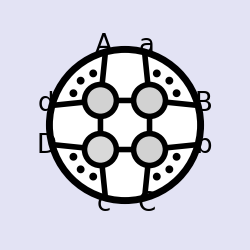
-Graphics-
One-Loop Amplitude Integrands
and Integrals in N=4 SYM
Jacob L. Bourjaily, 2013

```mathematica
SetDirectory[NotebookDirectory[]];
<<loop_amplitudes.m
```

```mathematica
Zs={{Sqrt[F1]S1,0,1/(Sqrt[F1]T1),T1/Sqrt[F1]},{1,0,0,0},{-S2/Sqrt[F2],0,0,S2/Sqrt[F2]},{-S2/Sqrt[F2],Sqrt[F2]/T2,-Sqrt[F2]/T2,S2/Sqrt[F2]+Sqrt[F2]/T2+Sqrt[F2] T2},{0,1/(Sqrt[F2]S2)+Sqrt[F2]/T2,-Sqrt[F2]/T2,Sqrt[F2]/T2},{0,1,0,0},{0,Sqrt[F1]/S1,1/(Sqrt[F1]T1),0}};MatrixForm[Zs]
```

(√F1 S1 | 0 | 1/(√F1 T1) | T1/(√F1)
1 | 0 | 0 | 0
-S2/(√F2) | 0 | 0 | S2/(√F2)
-S2/(√F2) | (√F2)/T2 | -(√F2)/T2 | S2/(√F2)+(√F2)/T2+√F2 T2
0 | 1/(√F2 S2)+(√F2)/T2 | -(√F2)/T2 | (√F2)/T2
0 | 1 | 0 | 0
0 | (√F1)/S1 | 1/(√F1 T1) | 0)

## Replacement rule versus //evaluate

```mathematica
ourReplacement=AB_ab:>Det[List@@(Zs⟦#⟧&/@AB)];
```

```mathematica
ab[1,2,4,5]/ab[2,3,5,6]//(#/.ourReplacement)-evaluate@#&
ourReplacement//FullForm
ab[2,3,5,6]//(#/.ourReplacement)-evaluate@#&
?evaluate
```

0

RuleDelayed[Pattern[AB,Blank[ab]],Det[Apply[List,Map[Function[Part[Zs,Slot[1]]],AB]]]]

0

Global`evaluate

Attributes[evaluate]={HoldFirst}
 
evaluate[exprn_]:=Block[{wExprn},ClearAll[ab,cap,kermit,Li,log];wExprn=ReleaseHold[exprn];ab[x___,cap[y_,z_,q___],w___]:=ab[x,cap[y,z,q],w]=If[Length[Join[y,z]]==5,(ab[x,#1,w]&)/@y.Apply[ab,RotateLeft[Partition[Join[y,z],4,1,1]]⟦1;;Length[y]⟧,{1}],Total[Apply[ab[x,#1,#2,w] ab@@Prepend[z,#3]&,Partition[y,3,1,1],{1}]]];ab[x___,shift[y_,z_],w___]:=ab[x,shift[y,z],w]=ab[x,y⟦1⟧,w]+z ab[x,y⟦2⟧,w];kermit[x_,y_]:=kermit[x,y]=-ab[A,B,cap[x,y]]^2/(Times@@Join@@(Apply[ab[A,B,##1]&,#1,{1}]&)/@{Partition[x,2,1,1],Partition[y,2,1,1]});wExprn=wExprn;ab[x__]:=ab[x]=Det[Zs⟦{x}/.{X1→-4,X2→-3,A→-2,B→-1}⟧];Li[x_]:=Li[x]=PolyLog[2,x];log[x_]:=log[x]=Log[x];wExprn=wExprn;ClearAll[ab,cap,kermit,Li,log];wExprn]

## Gluon Family

```mathematica
R1111tree=evaluate@superComponent[{1,2,3,4},{},{},{},{},{},{}]@treeAmp[7,1];
R1117tree=evaluate@superComponent[{1,2,3},{},{},{},{},{},{4}]@treeAmp[7,1];
R1177tree=evaluate@superComponent[{1,2},{},{},{},{},{},{3,4}]@treeAmp[7,1];
R1777tree=evaluate@superComponent[{1},{},{},{},{},{},{2,3,4}]@treeAmp[7,1];
R7777tree=evaluate@superComponent[{},{},{},{},{},{},{1,2,3,4}]@treeAmp[7,1];

Ffamily={R1111tree,R1117tree,R1177tree,R1777tree,R7777tree};
```

## Expansions and Universality

We now expand in T1 and T2 and divide by the leading term of the expansion.

```mathematica
Series[#,{T2,0,1},{T1,0,1}]/(Normal@Series[#,{T1,0,0},{T2,0,0}])&/@Ffamily//Expand//Collect[#,{T1,T2,F1,F2},FullSimplify]&
```

{1+T1 (-S1/(F1 (1+S1^2))-(S1 S2 T2)/(F1 F2 (1+S1^2) (S2^2+S1^2 (1+S2^2)))),1+T1 (-S1/(F1 (1+S1^2))-(S1 S2 T2)/(F1 F2 (1+S1^2) (S2^2+S1^2 (1+S2^2)))),1+T1 (-S1/(F1 (1+S1^2))-(S1 S2 T2)/(F1 F2 (1+S1^2) (S2^2+S1^2 (1+S2^2)))),1+T1 (-S1/(F1 (1+S1^2))-(S1 S2 T2)/(F1 F2 (1+S1^2) (S2^2+S1^2 (1+S2^2)))),1+T1 (-S1/(F1 (1+S1^2))-(S1 S2 T2)/(F1 F2 (1+S1^2) (S2^2+S1^2 (1+S2^2))))}

They are indeed the same after the normalization:

```mathematica
SameQ@@%
```

True

If we expand one order further in T1, we see that the degeneracy is lifted:

```mathematica
Series[#,{T2,0,1},{T1,0,2}]/(Normal@Series[#,{T1,0,0},{T2,0,0}])&/@Ffamily//Expand//Collect[#,{T1,T2,F1,F2},FullSimplify]&;
SameQ@@%
```

False

But it is not lifted at order T2^2 T1:

```mathematica
Series[#,{T2,0,2},{T1,0,1}]/(Normal@Series[#,{T1,0,0},{T2,0,0}])&/@Ffamily//Expand//Collect[#,{T1,T2,F1,F2},FullSimplify]&;
SameQ@@%
```

True

We make the replacement T1→α T1,F1→α F1, so that T1/F1 does not depend on α. So the leading term in the α expansion contains all terms with  T1/F1 fixed.

```mathematica
Normal@Series[#/(Normal@Series[#,{T1,0,0},{T2,0,0}])/.{T1->α T1,F1->α F1},{α,0,0}]&/@Ffamily//FullSimplify
SameQ@@%
```

{(F1 (S1 S2 T1 (F2 (1+S1^2) S2+S1^2 T2)+F1 (1+S1^2+T2^2) (S1^2 S2 T2+F2^2 S1^2 S2 T2+F2 (S2^2+S1^2 (1+S2^2+T2^2)))))/((S1 T1+F1 (1+S1^2+T2^2)) (S1 S2 T1 (F2 S2+T2)+F1 (S1^2 S2 T2+F2^2 S1^2 S2 T2+F2 (S2^2+S1^2 (1+S2^2+T2^2))))),(F1 (S1 S2 T1 (F2 (1+S1^2) S2+S1^2 T2)+F1 (1+S1^2+T2^2) (S1^2 S2 T2+F2^2 S1^2 S2 T2+F2 (S2^2+S1^2 (1+S2^2+T2^2)))))/((S1 T1+F1 (1+S1^2+T2^2)) (S1 S2 T1 (F2 S2+T2)+F1 (S1^2 S2 T2+F2^2 S1^2 S2 T2+F2 (S2^2+S1^2 (1+S2^2+T2^2))))),(F1 (S1 S2 T1 (F2 (1+S1^2) S2+S1^2 T2)+F1 (1+S1^2+T2^2) (S1^2 S2 T2+F2^2 S1^2 S2 T2+F2 (S2^2+S1^2 (1+S2^2+T2^2)))))/((S1 T1+F1 (1+S1^2+T2^2)) (S1 S2 T1 (F2 S2+T2)+F1 (S1^2 S2 T2+F2^2 S1^2 S2 T2+F2 (S2^2+S1^2 (1+S2^2+T2^2))))),(F1 (S1 S2 T1 (F2 (1+S1^2) S2+S1^2 T2)+F1 (1+S1^2+T2^2) (S1^2 S2 T2+F2^2 S1^2 S2 T2+F2 (S2^2+S1^2 (1+S2^2+T2^2)))))/((S1 T1+F1 (1+S1^2+T2^2)) (S1 S2 T1 (F2 S2+T2)+F1 (S1^2 S2 T2+F2^2 S1^2 S2 T2+F2 (S2^2+S1^2 (1+S2^2+T2^2))))),(F1 (S1 S2 T1 (F2 (1+S1^2) S2+S1^2 T2)+F1 (1+S1^2+T2^2) (S1^2 S2 T2+F2^2 S1^2 S2 T2+F2 (S2^2+S1^2 (1+S2^2+T2^2)))))/((S1 T1+F1 (1+S1^2+T2^2)) (S1 S2 T1 (F2 S2+T2)+F1 (S1^2 S2 T2+F2^2 S1^2 S2 T2+F2 (S2^2+S1^2 (1+S2^2+T2^2)))))}

True

r_tree function:

```mathematica
r[S1_,S2_,t1_,t2_]=(Normal@Series[(#/Normal@Series[#,{T1,0,0},{T2,0,0}])/.{T1->α T1,F1->α F1,T2->α T2,F2->α F2},{α,0,0}]&@R1111tree/.{T1->t1 F1,T2->t2 F2}//Simplify)
```

(S2^2+S1 S2^2 t1+S1^3 S2 t1 (S2+t2)+S1^4 (1+S2^2+S2 t2)+S1^2 (1+2 S2^2+S2 t2))/((1+S1^2+S1 t1) (S2^2+S1 S2 t1 (S2+t2)+S1^2 (1+S2^2+S2 t2)))

```mathematica
r[1,1,1,1]
```

11/18

## OPE expansion

The function expand gives all terms up to order t1^a t2^b with a+b=n

```mathematica
expand[n_][f___]:=(f/.{t1->α t1,t2->α t2}//Series[#,{α,0,n}]&//Normal)/.{α->1}//Collect[#,{t1,t2},FullSimplify]&
```

```mathematica
expansion=expand[5][r[S1,S2,t1,t2]]
```

1-(S1^5 t1^5)/((1+S1^2)^5)+t1^4 (S1^4/((1+S1^2)^4)+(S1^4 S2 (S1^6+4 S1^4 (1+S1^2) S2^2+6 (S1+S1^3)^2 S2^4+4 (1+S1^2)^3 S2^6) t2)/((1+S1^2)^4 (S2^2+S1^2 (1+S2^2))^4))+t1^3 (-S1^3/((1+S1^2)^3)-((S1^7 S2+3 S1^5 (1+S1^2) S2^3+3 S1^3 (1+S1^2)^2 S2^5) t2)/((1+S1^2)^3 (S2^2+S1^2 (1+S2^2))^3)+((-S1^7 S2^2-4 S1^5 (1+S1^2) S2^4+3 S1^3 (-1+S1^2) (1+S1^2)^2 S2^6) t2^2)/((1+S1^2)^3 (S2^2+S1^2 (1+S2^2))^4))+t1^2 (S1^2/((1+S1^2)^2)+((S1^4 S2+2 S1^2 (1+S1^2) S2^3) t2)/((1+S1^2)^2 (S2^2+S1^2 (1+S2^2))^2)+((S1^4 S2^2-S1^2 (-1+S1^2+2 S1^4) S2^4) t2^2)/((1+S1^2)^2 (S2^2+S1^2 (1+S2^2))^3)+((-S1^6 (2+S1^2) S2^3+2 S1^4 (-1+S1^4) S2^5) t2^3)/((1+S1^2)^2 (S2^2+S1^2 (1+S2^2))^4))+t1 (-S1/(1+S1^2)-(S1 S2 t2)/((1+S1^2) (S2^2+S1^2 (1+S2^2)))+(S1^3 S2^2 t2^2)/((1+S1^2) (S2^2+S1^2 (1+S2^2))^2)-(S1^5 S2^3 t2^3)/((1+S1^2) (S2^2+S1^2 (1+S2^2))^3)+(S1^7 S2^4 t2^4)/((1+S1^2) (S2^2+S1^2 (1+S2^2))^4))

```mathematica
f[a_,b_][S1_,S2_]:=Coefficient[expansion,t1^a t2^b]
```

```mathematica
Integrate[x^(2a-1)/((x^2+1)^b),{x,0,∞},GenerateConditions->False]
```

(Gamma[a] Gamma[-a+b])/(2 Gamma[b])

## Comparison with Integrability

### Fourier Function

The function fourier:

```mathematica
fourier[X__]:=((4 S1^(2 ⅈ u)/(S1 S2)(S2^(2 ⅈ v) X/.{S2->(S2 S1)/(√(1+S1^2))})//Simplify//PowerExpand)//Expand)/.{S2^(k_.)(1+S2^2)^(n_.):>(Gamma[(k+1)/2] Gamma[(-(k+1))/2-n])/(2 Gamma[-n])}/.{S1^(k_.)(1+S1^2)^(n_.):>(Gamma[(k+1)/2] Gamma[(-(k+1))/2-n])/(2 Gamma[-n])}//Simplify
```

### Comparision with 1407.1736:

```mathematica
h[a_][u_]=(u^2+a^2/4)/g^2;
μ[a_][u_]=(-1)^a g^2(Gamma[a/2+I u]Gamma[a/2-I u])/((a^2/4+u^2)Gamma[a]);
P[a_,b_][u_,v_]=(-1)^b(a/2-I u)(b/2+I v)(Gamma[(a-b)/2+I u-I v]Gamma[(a+b)/2-I u+I v])/(g^2 Gamma[a/2+I u]Gamma[b/2-I v]Gamma[1+(a-b)/2-I u+I v]);
```

```mathematica
Table[(fourier@f[a,b][S1,S2]/.{u->-u,v->-v})/(h[a][u]μ[a][u]P[a,b][-u,v]μ[b][v])//FullSimplify,{a,4},{b,5-a}]//TableForm
```

1 | 1 | 1 | 1
1 | 1 | 1 | 
1 | 1 |  | 
1 |  |  |